## Working with Reaction-Diffusion Equations Using Mathematica

### These exercises will expose you to two of the things Mathematica does really well: Symbolic math, and dynamic visualization.

You will also learn how natural it is to use the Notebook format in Mathematica, which has a lot of ability to format things nicely (like Latex, only easier).

## 1. What are reaction-diffusion equations?

These are partial differential equations that describe systems in which species (i.e. molecules) both diffuse and undergo biochemical reactions.  For simplicity, we will consider only one-dimensional diffusion here, in which case the PDE that describes the dynamics of such diffusion is:   (∂c)/(∂t) = D (∂^2 c)/(∂x^2)  (Fick’s second law), where c is the amount or concentration of the species of interest.  In contrast, reactions are typically modeled with ODEs like:

ⅆc/ⅆt= v  (with v a constant, constant production);
ⅆc/ⅆt= -k c  (first order destruction);
ⅆc/ⅆt= -k a c (reaction of c with a to form something else)
ⅆc/ⅆt= v/(1+ γ c) (negative feedback of c on its own production)

To generate reaction diffusion equations one simply sums up the terms on the right hand side for whatever processes are going on in ones system (this is called the principle of superposition).  Thus, diffusion with constant production and first order decay (destruction) looks like this:

(∂c)/(∂t) = D(∂^2 c)/(∂x^2) + v - k c

Solving RD equations requires specifying both initial conditions (the value of c everywhere at t=0) and boundary conditions, the value of either c or (∂c)/(∂x) at two points, representing the boundaries of the system.  Examples of boundary conditions can be that c has a constant value, or constant derivative at a given boundary, but can also be more complicated.  Also, one can consider an infinite domain, where c can diffuse to infinity; typically solving PDEs for such cases requires solving with an arbitrary boundary and after getting a solution, letting the location of it go to infinity.  

We will use Mathematica to generate some analytical solutions to some RD equations.  In some cases, however, explicit solutions may be hard to find, in which case we can also solve equations numerically, substituting in parameter values before solving, and getting a solution in the form of a graph of how the system behaves.

## 2. Representing PDEs in Mathematica

Everything you type in Mathematica that starts with a letter is interpreted as a “symbol”, unless it is already defined as something else (like a function).  All the pre-defined functions start with a capital letter, so as long as you name things using a lower case letter as the first letter, there will be no problem.

How does Mathematica let you know if you’ve typed something that already has a definition associated with it?

Representing variables versus parameters:  Mathematica will happily do math with any symbol you choose to type, but if you want it to take the derivative of a variable, you must explicitly show what that variable is a function of.

So if you write “c” and then take the derivative of it with respect to x, you will get zero.
But if you write c[x] and then take the derivative of it with respect to x, you will get c'[x].
Note that Mathematica typically uses square brackets where typeset Math with typically use parenthesis.  

The function that represents taking a derivative in Mathematica is “D”.  The syntax is 

D[var_, arg1_, arg2_, arg3_...]
or
D[var_, {arg1_, times_}, {arg2_, times_}, {arg3_, times_}...]

where  “var” is the variable, “args” are the arguments you are taking derivatives with respect to , and times” means how many times you are taking the derivative (i.e. second derivative, third derivative) etc.

How would you represent ⅆc/ⅆt in Mathematica?

How would you represent (∂^2 c)/(∂x ∂y) in Mathematica?

Another way to produce these forms is using the following syntax: 

Derivativepaclet:ref/Derivative[n_1,n_2,…][f] 
is the general form, representing a function obtained from f by differentiating n_1 times with respect to the first argument, n_2 times with respect to the second argument, and so on.

For example:

```mathematica
Derivative[1,1][c]
```

c^(1,1)

```mathematica
Derivative[1,1][c][x,y]
```

c^(1,1)[x,y]

Finally to write any equation in Mathematica, you will need to know what symbol to use for “logical equals”.  Mathematica uses a double equals sign. If you use a single equals sign it is an instruction to set the symbol on the left to have the value on the right.  If you use a double equals it means that you have an equation you are considering.  An equation is like a question:  Does the right hand side evaluate to the same thing as the left hand side?  In the event that you write an equation that is tautologically true in Mathematica, it just returns “True”

```mathematica
5==5
```

```mathematica
a+b==b+a
```

```mathematica
√(5^2)==5
```

```mathematica
2== Log[10,100]
```

But sometimes it may needs some instruction before it can be sure that something is a tautology

```mathematica
√(x^2)==x
```

```mathematica
Assuming[Element[x, Reals], Simplify[√(x^2)==Abs[x]]]
```

Exercise:  write the PDE  (∂c)/(∂t) = (∂^2 c)/(∂x^2) + v - k c in Mathematica.

## 3. Analytical Solutions to PDEs

Consider this example.  Give it some time to run:

```mathematica
DSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}, c[x,t], {x, t}]
```

{{c[x,t]→2 (2 ⅇ^(-1/4 d π^2 t (1+2 K[1])^2) Cos[π K[1]] Cos[1/2 π x (1+2 K[1])])/(π+2 π K[1])K[1]0∞}}

This is an alternate form:

```mathematica
DSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}, c, {x, t}]
```

{{c→Function[{x,t},2 (2 ⅇ^(-1/4 d π^2 t (1+2 K[1])^2) Cos[π K[1]] Cos[1/2 π x (1+2 K[1])])/(π+2 π K[1])K[1]0∞]}}

What’s with this “{{symbol-> formula}}” formatting?  What does it mean?  Why is the Summation operator inactive?

```mathematica
With[{d=0.5, n=5},Plot3D[Activate[2 (2 ⅇ^(-1/4 d π^2 t (1+2 K[1])^2) Cos[π K[1]] Cos[1/2 π x (1+2 K[1])])/(π+2 π K[1])K[1]0n], {x, 0,1}, {t, 0, 5}]]
```

-Graphics3D-

```mathematica
With[{d=0.5, n=20},Plot3D[Activate[2 (2 ⅇ^(-1/4 d π^2 t (1+2 K[1])^2) Cos[π K[1]] Cos[1/2 π x (1+2 K[1])])/(π+2 π K[1])K[1]0n], {x, 0,1}, {t, 0, 5}, PlotRange-> All]]
```

-Graphics3D-

## 4. Analytical Solutions to ODEs that represent steady-states of reaction diffusion PDEs

Sometimes we are interested in the long-time solutions to RD equations.  We may set time rates to zero, and then our PDEs become ODEs.  For example:

```mathematica
(∂c)/(∂t) = (∂^2 c)/(∂x^2)  - k c
```

becomes

```mathematica
0 == d c''[x] - k c[x]
```

For functions of one variable, Mathematica can recognize the “prime” notation, i.e. c’’[x] is just as good as the more cumbersome c^(2)[x]

Can we use DSolve to solve this?  We still need boundary conditions, but no longer need an initial condition.

```mathematica
DSolve[{0 == d c''[x]  - k c[x], c[0]==  1,c[1] ==0}, c[x], x]
```

{{c[x]→-(ⅇ^(-(√k x)/(√d)) (-ⅇ^((2 √k)/(√d))+ⅇ^((2 √k x)/(√d))))/(-1+ⅇ^((2 √k)/(√d)))}}

```mathematica
FullSimplify[-(ⅇ^(-(√k x)/(√d)) (-ⅇ^((2 √k)/(√d))+ⅇ^((2 √k x)/(√d))))/(-1+ⅇ^((2 √k)/(√d))), d>0&&k>0]
```

-Csch[√(k/d)] Sinh[√(k/d) (-1+x)]

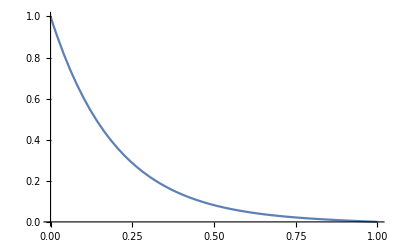

```mathematica
With[{λ=0.2},Plot[-Csch[1/λ] Sinh[ (-1+x)/λ], {x, 0, 1}]]
```

Can you use DSolve to solve the steady state of this, with the boundary condition that c=1 at x=0 and c=0 at infinity

```mathematica
(∂c)/(∂t) = (∂^2 c)/(∂x^2)  +v - k c
```

What does Mathematica do if you leave out one of the boundary conditions?  What if you use a symbol as a boundary condition?  How does it handle it?

What about this, which represents an example of saturable decay, as might occur if decay requires binding to a receptor that is in limiting supply:

```mathematica
(∂c)/(∂t) = (∂^2 c)/(∂x^2)  +v - k c/(1+c)
```

Mathematica will not always find solutions even when they exist.  Consider this example:

```mathematica
DSolve[{0 == d c''[x] - k c[x]^2, c[0]==c0, c[1] ==0}, c[x], x]
```

Can you use some classical math tricks to help Mathematica out?

```mathematica
d c''[x] ==  k c[x]^2
```

```mathematica
d c''[x]c'[x] ==  k c[x]^2 c'[x]
```

```mathematica
Integrate[ d c''[x]c'[x] , x] == Integrate[k c[x]^2 c'[x], x]+K[1]
```

1/2 d c'[x]^2==1/3 k c[x]^3+K[1]

Because we know that c’[x] and c[x] will both approach zero as x gets to infinity, then if one of our boundary conditions is x=infinity, that’s equivalent to saying that K[1] has to be zero.  We insert an arbitrary symbol “c0” to mean c[x] at x=0, and then solve

```mathematica
DSolve[{1/2 d c'[x]^2==1/3 k c[x]^3, c[0]==c0}, c[x], x]
```

{{c[x]→(6 c0 d)/(6 d-2 √6 √c0 √d √k x+c0 k x^2)},{c[x]→(6 c0 d)/(6 d+2 √6 √c0 √d √k x+c0 k x^2)}}

```mathematica
FullSimplify[Flatten[c[x]/.DSolve[{1/2 d c'[x]^2==1/3 k c[x]^3, c[0]==c0}, c[x], x]], d>0&&k>0]
```

{(6 c0 d)/(6 d+x (-2 √6 √(c0 d k)+c0 k x)),(6 c0 d)/(6 d+x (2 √6 √(c0 d k)+c0 k x))}

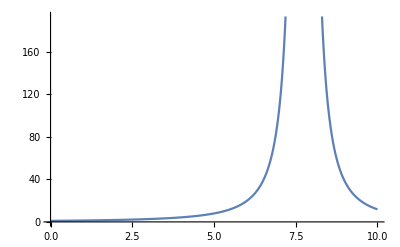

```mathematica
With[{d=1, k=0.1, c0=1},Plot[(6 c0 d)/(6 d+x (-2 √6 √(c0 d k)+c0 k x)), {x, 0, 10}]]
```

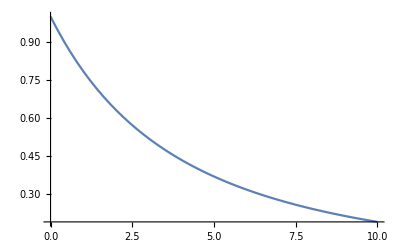

```mathematica
With[{d=1, k=0.1, c0=1},Plot[(6 c0 d)/(6 d+x (2 √6 √(c0 d k)+c0 k x)), {x, 0, 10}]]
```

Although Mathematica’s ability to FullSimplify things is impressive, it won’t always find the “prettiest” form

```mathematica
FullSimplify[(6 c0 d)/(6 d+x (2 √6 √(c0 d k)+c0 k x)),  c0>0&&d>0&&k>0]
```

(6 c0 d)/(6 d+x (2 √6 √(c0 d k)+c0 k x))

Manually rearranging we can do better

```mathematica
FullSimplify[c0/(1+ x √((k c0)/(6 d)))^2== (6 c0 d)/(6 d+x (2 √6 √(c0 d k)+c0 k x)), c0>0&&d>0&&k>0]
```

True

This tells us that, for large enough x, the curve approaches something proportional to 1/x^2.

Use the same approach to solve:
0 == d c''[x] - k c[x]^4, with boundary conditions c[0]==c0, c[∞] ==0, for c[x]

## 5. Numerical Solutions to PDEs and ODEs

Lot’s of PDEs defy easy analytical solution, but can be plotted numerically.  Consider the first one we solved above

```mathematica
With[{d=0.5},NDSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}, c[x,t], {x,0,1}, {t, 0, 10}]]
```

Why the error message when you run this?

```mathematica
With[{d=0.5},With[{solu=Flatten[NDSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}, c[x,t], {x,0,1}, {t, 0, 10}]]},
Plot3D[c[x,t]/.solu, {x, 0, 1}, {t, 0, 10}]]]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

-Graphics3D-

```mathematica
With[{d=2, k=0.2, v=0.1},With[{solu=Flatten[NDSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t]+v- k c[x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}, c[x,t], {x,0,1}, {t, 0, 10}]]},
Plot3D[c[x,t]/.solu, {x, 0, 1}, {t, 0, 10}, PlotRange-> All]]]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

-Graphics3D-

We can also do numerical solutions to ODEs that we got from steady state reaction diffusion equations, but weren’t able to solve analytically.

```mathematica
DSolve[{0 == d c''[x] - k c[x]/(1+c[x]), c[0]==c0, c[1] ==0}, c[x], x]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

How would we do this numerically?

```mathematica
With[{d=1, k=0.1, c0=0.1}, Flatten[NDSolve[{0 == d c''[x] - k c[x]/(1+c[x]), c[0]==c0, c[10] ==0}, c[x], {x, 0, 2}]]]
```

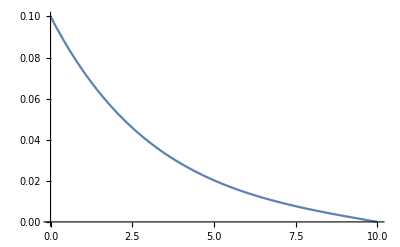

```mathematica
With[{d=1, k=0.1, c0=0.1}, With[{solu=Flatten[NDSolve[{0 == d c''[x] - k c[x]/(1+c[x]), c[0]==c0, c[10] ==0}, c[x], {x, 0, 10}]]}, 
Plot[c[x]/.solu, {x, 0,10}]]]
```

```mathematica
Manipulate[With[{solu=Flatten[NDSolve[{0 == d c''[x] - k c[x]/(1+c[x]), c[0]==c0, c[10] ==0}, c[x], {x, 0, 10}]]}, 
Plot[c[x]/.solu, {x, 0,10}]], {{d,1},0,4},{{k,0.1},0,2},{{c0,0.1},0,2}]
```

```mathematica
Manipulate[With[{solu=Flatten[NDSolve[{0 == d c''[x] - k c[x]/(1+c[x]), c[0]==c0, c[xmax] ==0}, c[x], {x, 0, xmax}]]}, 
Plot[c[x]/.solu, {x, 0,xmax}]], {{d,1},0,4},{{k,0.1},0,2},{{c0,0.1},0,2}, {{xmax,10},1,20}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 9.12404×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

We notice that numerically solving the second order ODE creates some difficulties for some parameter values.  Especially if xmax gets too big.  

There’s an alternative way to get a steady state solution which is often numerically easier:  Find the numerical solution for the original PDE and then increase time until the result stops changing.  

Let’s compare.  In this case, the PDE that the above was the steady stead of was:

```mathematica
(∂c)/(∂t) = (∂^2 c)/(∂x^2)  - k c/(1+c)
```

in other words:

```mathematica
D[c[x,t],t] == d D[c[x,t], {x,2}]  - k c[x,t]/(1+c[x,t])
```

c^(0,1)[x,t]==-(k c[x,t])/(1+c[x,t])+d c^(2,0)[x,t]

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

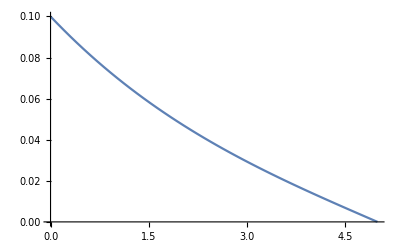

```mathematica
With[{k=0.1, d=1, c0=0.1, xmax=5, tmax=100},
Plot[Evaluate[c[x,tmax]/.Flatten[NDSolve[{Derivative[0,1][c][x,t]==-(k c[x,t])/(1+c[x,t])+d Derivative[2,0][c][x,t], c[0,t]==c0, c[xmax,t] ==0, c[x, 0]== 0}, c, {x,0,xmax}, {t, 0, tmax}]]], {x, 0, xmax}]]
```

We can turn off error messages if we like, with “Quiet”

```mathematica
With[{k=0.1, d=1, c0=0.1, xmax=5, tmax=100},
Plot[Evaluate[c[x,tmax]/.Flatten[Quiet[NDSolve[{Derivative[0,1][c][x,t]==-(k c[x,t])/(1+c[x,t])+d Derivative[2,0][c][x,t], c[0,t]==c0, c[xmax,t] ==0, c[x, 0]== 0}, c, {x,0,xmax}, {t, 0, tmax}]]]], {x, 0, xmax}]]
```

-Graphics-

Or we can change the initial condition so that it’s consistent at x=0 and x=xmax with the boundary conditions

```mathematica
With[{k=0.1, d=1, c0=0.1, xmax=5, tmax=100},
Plot[Evaluate[c[x,tmax]/.Flatten[NDSolve[{Derivative[0,1][c][x,t]==-(k c[x,t])/(1+c[x,t])+d Derivative[2,0][c][x,t], c[0,t]==c0, c[xmax,t] ==0, c[x, 0]== c0(1-x/xmax)}, c, {x,0,xmax}, {t, 0, tmax}]]], {x, 0, xmax}]]
```

-Graphics-

```mathematica
Manipulate[Plot[Evaluate[c[x,tmax]/.Flatten[Quiet[NDSolve[{Derivative[0,1][c][x,t]==-(k c[x,t])/(1+c[x,t])+d Derivative[2,0][c][x,t], c[0,t]==c0, c[xmax,t] ==0, c[x, 0]==c0(1-x/xmax)}, c, {x,0,xmax}, {t, 0, tmax}]]]], {x, 0, xmax}], {{d,1},0,4},{{k,0.1},0,2},{{c0,0.1},0,2}, {{xmax,10},1,20}, {{tmax,100},1, 200}]
```

Manipulate is a very useful function, that is not limited to just two-D plots.  Moreover, almost anything can be put on a controller, and controllers can have various forms

```mathematica
Manipulate[Plot3D[Evaluate[c[x,tmax]/.Flatten[Quiet[NDSolve[{Derivative[0,1][c][x,t]==-(k c[x,t])/(1+c[x,t])+d Derivative[2,0][c][x,t], c[0,t]==c0, c[xmax,t] ==0, c[x, 0]==c0(1-x/xmax)}, c, {x,0,xmax}, {t, 0, tmax}]]]], {x, 0, xmax}, {t, 0, tmax}], {{d,1},0,4},{{k,0.1},0,2},{{c0,0.1},0,2}, {{xmax,10},1,20}, {{tmax,100},1, 200}]
```

```mathematica
Manipulate[Plot3D[Evaluate[c[x,tmax]/.Flatten[Quiet[NDSolve[{Derivative[0,1][c][x,t]==-(k c[x,t]^n)/(1+c[x,t]^n)+d Derivative[2,0][c][x,t], c[0,t]==c0, c[xmax,t] ==0, c[x, 0]==c0(1-x/xmax)}, c, {x,0,xmax}, {t, 0, tmax}]]]], {x, 0, xmax}, {t, 0, tmax}, AxesLabel-> {"x", "time", "c"}], {n, {1,2,3,4,5}},{{d,1},0,4},{{k,0.1},0,2},{{c0,0.1},0,2}, {{xmax,10},1,20}, {{tmax,100},1, 200}]
```

## More complicated forms

#### NDSolve can handle equations with piecewise functions.

For example, suppose we had a molecule produced from x=0 to x=1, but be able to diffuse anywhere in a larger domain. Instead of our production term being a constant, “v”, it can be an “if” statement: 

If[x>1, v, 0]

Exercise :  Solve a RD equation on a domain 0<x<10,  for a molecule that’s produced only between x=0 and x=1, and is destroyed everywhere with a rate constant “k” that is also not uniform, but is in fact twice as high for x>4 than it is for 0<x<4.

Have the boundary conditions be (1) that the derivative of c with respect to x is zero at x=0, and (2) that c is zero at x=10.  

Pick some parameters, or pick parameter ranges and put them on sliders

#### NDSolve can handle systems of equations.

As long as only one of the equations is a PDE, Mathematica can handle almost any number of ODEs coupled to it.  Consider the following system:  Species c diffuses, but it binds reversibly to immobile species r to form the immobile complex cr.  There is no degradation of c, just cr and r, which occurs with constant probability per unit time.  Species r is produced at a constant rate.  

To describe this system, we need three equations--one for c, r, and cr.  Only the one for c is truly a PDE because only it has diffusion in it, but in order to write down the whole system in a consistent way we must still make every variable of function of both x and t, so every equation is still written as a PDE.  

Each equation has  a time rate of change on the left hand side, and reaction (plus diffusion in the case of c) on the right hand side.  

For r the reaction terms would be production (a constant), destruction (a constant multiplied by r[x,t]) binding to c (a constant times r[x,t] times c[x,t]) and unbinding from cr (a constant times cr[x,t]).

For c the reaction terms would be binding between c and r, and unbinding from cr (the same terms as used above).  There’d also be the usual diffusion term.

For cr the reaction terms would be binding between c and r, unbinding from cr, and destruction of cr (a constant times cr[x,t].  Note that when a reaction makes a species go away, you use a negative sign; when it makes it appear you use a positive sign.  

Once you have written this out as a list of three equations (lists are surrounded by curly brackets and elements are separated by commas), you need to add initial and boundary conditions.  You need initial conditions for every species (c, r, cr) because they all change over time.  You only need boundary conditions for one species (c) because only it diffuses.  

We will use boundary conditions for c at x=0 of 1, and at xmax =0, where xmax is a parameter that you can give a value to later.  For initial conditions we will use c = 1-x/xmax, i.e. a straight line from {0,1} to {xmax, 0}; r=0 and cr=0.  

When you use NDSolve now, you will ask NDSolve to produce a list of results, {c[x,t], r[x,t], cr[x,t]}, so you will have three things you can possibly plot.  If you name your solution list something like “solu”, then the syntax 

c[x,t]/.solu

retrieves the c-interpolation function, which you can plot.

## Some useful tips about Plotting and Manipulating

The syntax of “Plot” and “Plot3D” is 
Plot[function, domain, options].  or
Plot[{list of functions}, domain, options]. in which case various functions are plotted together on the same plot

There are many options you can put in there, and using the function browser can help you learn what they are.  Examples are

PlotRange-> All (include all datapoints; the default setting will often truncate plot range so places where not much is happening are cut off)
PlotRange-> {0, Automatic} (makes sure the plot starts from 0, but let’s mathematic choose the upper bound)
PlotStyle-> Red (make the curve red)
PlotStyle-> {Red, Green, Blue} (makes the curves for multiple functions red, green, blue in that order)
PlotLegends-> Automatic (puts legends on your plot so that curves can be identified, where the legends are the expressions you are plotting.
PlotLegends-> {lbl_1,lbl_2,…}(puts legends on your plot that correspond to the text labels you give it ( lbl_i, etc.).  Note that when specifying text you should put “ “ marks around it; otherwise if you type something that has a value assigned to it, Mathematica will display the value and not the text.

If you have multiple functions and are happy plotting them on top of one another then putting them all together in one Plot command is fine, but if they have different ranges, they may not look pretty that way.  So another option is to use “GraphicsRow” and “GraphicsGrid” to format multiple plots in a row or grid.  Evaluate these examples to see

```mathematica
GraphicsRow[{Plot[Sin[x], {x, 0, 4}], Plot[Sin[x]^2, {x, 0, 4}],Plot[Sin[x]^3, {x, 0, 4}]}]
```

```mathematica
GraphicsGrid[{{Plot[Sin[x], {x, 0, 4}], Plot[Sin[x]^2, {x, 0, 4}],Plot[Sin[x]^3, {x, 0, 4}]},{Plot[Cos[x], {x, 0, 4}], Plot[Cos[x]^2, {x, 0, 4}],Plot[Cos[x]^3, {x, 0, 4}]},{Plot[Tan[x], {x, 0, 4}], Plot[Tan[x]^2, {x, 0, 4}],Plot[Tan[x]^3, {x, 0, 4}]}}]
```

You can even use such code inside Manipulate

```mathematica
Manipulate[
GraphicsGrid[{{Plot[Sin[x], {x, 0, xmax}], Plot[Sin[x]^2, {x, 0,xmax}],Plot[Sin[x]^3, {x, 0,xmax}]},{Plot[Cos[x], {x, 0, xmax}], Plot[Cos[x]^2, {x, 0,xmax}],Plot[Cos[x]^3, {x, 0,xmax}]},{Plot[Tan[x], {x, 0, xmax}], Plot[Tan[x]^2, {x, 0, xmax}],Plot[Tan[x]^3, {x, 0, xmax}]}}], {{xmax,4}, 0, 10}]
```

Note that things that are repeated many times can be handled more compactly by giving them names

```mathematica
Manipulate[With[{pr={x,0,xmax}},
GraphicsGrid[{{Plot[Sin[x],pr], Plot[Sin[x]^2,pr],Plot[Sin[x]^3, pr]},{Plot[Cos[x],pr], Plot[Cos[x]^2,pr],Plot[Cos[x]^3,pr]},{Plot[Tan[x],pr], Plot[Tan[x]^2,pr],Plot[Tan[x]^3,pr]}}]], {{xmax,4}, 0, 10}]
```

We can make things even more compact, by noting that the form Plot[__, pr] keeps appearing over and over.  We can in effect define a function on the fly that represents Plot[#, pr], where # stand for something to be filled in, and then use that as an operator over a list of things to fill in.  The “&” symbol is used to denote that the thing to the left of it is a function with a slot to be filled in.  The function Map applies this function to every element in a list.

```mathematica
GraphicsRow[Map[Plot[#, {x,0,5}]&,{Sin[x], Sin[x]^2, Sin[x]^3, Sin[x]^4}]]
```

Even the list {Sin[x], Sin[x]^2, Sin[x]^3, Sin[x]^4} can be written more compactly as

```mathematica
Table[Sin[x]^n, {n, 1, 4}]
```

{Sin[x],Sin[x]^2,Sin[x]^3,Sin[x]^4}

See how compactly we can write the instructions to make 12 plots:

```mathematica
GraphicsGrid[Map[Plot[#, {x,0,5}]&,{Table[Sin[x]^n, {n, 1, 4}],Table[Cos[x]^n, {n, 1, 4}],Table[Tan[x]^n, {n, 1, 4}]},{2}]]
```

Did you note the “{2}” we slipped in at the end of the Map function.  It tells map to apply the function at “level 2”, i.e. since we have a list of lists, the actual elements of the list are two levels down.  

Finally, we can make this even more compact:

```mathematica
GraphicsGrid[Map[Plot[#, {x,0,5}]&,Map[Table[#, {n,1,4}]&, {Sin[x]^n, Cos[x]^n, Tan[x]^n}],{2}]]
```

There’s an alternate “prefix” way to write Map, which involves fewer keystrokes, that we can use when we don’t have to explicitly tell Mathematica what level to map at.

```mathematica
GraphicsGrid[Map[Plot[#, {x,0,5}]&,Table[#, {n,1,4}]&/@ {Sin[x]^n, Cos[x]^n, Tan[x]^n},{2}]]
```